SP⋆ Connection

$SPProjDir::usage="Current sprectrum assignment directory";
$SPDir::usage="sp binary location";
$SP::usage="Default SPManager from $SPDir";
$SPCAT::usage="Default SPCAT";
$SPFIT::usage="Default SPFIT";

$VARFile::usage=".var file for the current project";
$PARFile::usage=".par file for the current project";
$LINFile::usage=".lin file for the current project";

Build

SPBuild::usage="Downloads the SP stuff if necessary and compiles the C code (Unix only)";

Run

SPManager::usage="Useful little wrapper";
SPCall::usage="General call function for calling spfit or spcat";
SPRun::usage="Runs SPCall on fit, then cat, then opens the var file 
(end action may change in the future)";
SPRunStrings::usage=
	"Sends strings to spcat and spfit and returns the string output";

IO

SPio::usage="Input/Ouput formatter for SPFIT/SPCAT";

SPChanges::usage=
	"Uses git diff to find differences in files across backups";

Viewer

SPViewer::usage=
	"An interactive viewer for spfit/spcat calculations";

PAR

$SPParIDUsageInfo::usage=
	"A dict of usage info for the various components of a parameter ID";

SPParBuildID::usage=
	"Builds a parameter ID";
SPParParseID::usage=
	"Parses a parameter ID";

$SPParConstantMap::usage=
	"A collection of constants and their ID numbers";
SPParSelectID::usage=
	"Selects the appropriate ID for a given constant";

SPParFile::usage=
	"Generates a par file string from a set of specs";
SPParConfig::usage=
	"Generates a par file config from a set of atoms and specs";

INT

SPIntBuildFlags::usage="";
SPIntParseFlags::usage="";

SPIntBuildID::usage="";
SPIntParseID::usage="";

SPIntFile::usage="Formats a .int file";
SPIntConfig::usage="Returns a config association for a set of atoms";

Begin["`Private`"];

Globals

$SPProjDir=None;
$SPDir=ChemExtension["sp"];
$SP:=SPManager[$SPDir];
$SPCAT:=SPManager[$SPDir,"spcat"];
$SPFIT:=SPManager[$SPDir,"spfit"];

$VARFile:=Replace[$SPProjDir,s_String:>s<>".var"];
$PARFile:=Replace[$SPProjDir,s_String:>s<>".par"];
$LINFile:=Replace[$SPProjDir,s_String:>s<>".lin"];

Download and make (Unix)

$SPHOME="http://spec.jpl.nasa.gov/ftp/pub/calpgm";
$SPFILES="*.c"|"*.h"|"Makefile";

spdownloadFileNames[pat_:$SPFILES]:=
	Select[
		URLParse[#,"Path"][[-1]]&/@
			Replace[$SPFILEURLS,	
				Except[{__String}]:>
					(
						$SPFILEURLS=
							Cases[
								Import[$SPHOME,{"HTML","XMLObject"}],
								XMLElement["a",{___,"href"→f_,___},_]:>
									StringTrim[f,$SPHOME],
								∞
								]
						)
				],
		StringMatchQ[$SPFILES]
		]

SPDownload[dir_:Automatic]:=
	With[{d=Replace[dir,Automatic→$SPDir]},
		If[!DirectoryQ@d,CreateDirectory[d]];
		If[!FileExistsQ@FileNameJoin@{d,"Makefile"},
			URLDownload[
				URLBuild@{$SPHOME,#},
				FileNameJoin@{d,#}]&/@spdownloadFileNames[],
			d
			]
	];

SPBuild::make="``";
SPBuild[dir_:Automatic]:=
	With[{d=Replace[dir,Automatic→$SPDir]},
		If[!FileExistsQ@FileNameJoin@{d,"Makefile"},SPDownload@d];
		SetDirectory@d;
		With[{r=RunProcess@{"make","-f",FileNameJoin@{d,"Makefile"}}},
			ResetDirectory[];
			If[r["StandardError"]=!="",Message[SPBuild::make,r["StandardError"]]];
			If[r["StandardOutput"]=!="",Message[SPBuild::make,r["StandardOutput"]]];
			If[r["ExitCode"]=!=0,
				$Failed,
				SPManager[d]
				]
			]
		];

SPDownloadFile[f_,dir:_String?DirectoryQ|Automatic|None:Automatic]:=
	With[{path=
		If[URLParse[f]["Scheme"]===None,
			If[Length@URLParse[f]["Path"]==0||URLParse[f]["Domain"]===None,
				URLBuild@{ChemTools`Private`$SPHOME,f},
				URLBuild@Merge[{"Scheme"->"https",URLParse@f},First]
				],
			f
			],
		d=Replace[dir,{Automatic→"~/Desktop",None→$TemporaryDirectory}]},
		URLDownload[path,FileNameJoin@{d,Last@URLParse[path]["Path"]}]
		];

Run stuff

runBasic

runBasic[cmd_,file_?FileExistsQ]:=(
	SetDirectory@DirectoryName@file;
	With[{r=
		RunProcess@{
			If[
				StringContainsQ[cmd,$PathnameSeparator],
				ExpandFileName@cmd,
				cmd
				],
			FileNameTake@file}},
		ResetDirectory[];
		If[StringLength@r["StandardError"]>0,
			Message[SPRun::err,r["StandardError"]]
			];
		If[StringLength@r["StandardOutput"]>0,
			Message[SPRun::out,r["StandardOutput"]]
			];
		With[{d=DirectoryName@file,b=FileBaseName@file},
			Merge[{
				r,
				"PAR"→
					Replace[FileNameJoin@{d,b<>".par"},Except[_String?FileExistsQ]→None],
				"LIN"→
					Replace[FileNameJoin@{d,b<>".lin"},Except[_String?FileExistsQ]→None],
				"VAR"→
					Replace[FileNameJoin@{d,b<>".var"},Except[_String?FileExistsQ]→None],
				"INT"→
					Replace[FileNameJoin@{d,b<>".int"},Except[_String?FileExistsQ]→None],
				"CAT"→
					Replace[FileNameJoin@{d,b<>".cat"},Except[_String?FileExistsQ]→None],
				"OUT"→
					Replace[FileNameJoin@{d,b<>".out"},Except[_String?FileExistsQ]→None],
				"STR"→
					Replace[FileNameJoin@{d,b<>".str"},Except[_String?FileExistsQ]→None],
				"EGY"→
					Replace[FileNameJoin@{d,b<>".egy"},Except[_String?FileExistsQ]→None]
				},
				Last
				]
			]
		]
	)

fitCall

createArc[file_]:=
	With[{
		dir=If[DirectoryQ@file,file,DirectoryName@file],
		base=FileBaseName@file,tmp=CreateDirectory[]},
		With[{fs=FileNameJoin@{dir,base<>"."<>#}&/@{"par","var","lin"}},
			CopyFile[#,FileNameJoin@{tmp,FileNameTake@#}]&/@fs;
			If[!FileExistsQ@FileNameJoin@{dir,"Backups"},
				CreateDirectory@FileNameJoin@{dir,"Backups"}];
			CreateArchive[tmp,
				FileNameJoin@{
					dir,
					"Backups",
					DateString@{
						"Month","-","Day","-","Year","_",
						"Hour","-","Minute","-","Second"}<>".zip"
					}]
			]
		];

fitCall[spfit_,file_,arc_:True]:=
	With[{f=FileNameJoin@{
		If[DirectoryQ@file,file,DirectoryName@file],
		FileBaseName@file<>".par"}},
		If[arc,createArc@file];
		runBasic[spfit,f]
		];

catCall

catCall[spcat_,file_]:=
	With[{f=
		FileNameJoin@{If[DirectoryQ@file,file,DirectoryName@file],FileBaseName@file<>".var"}
		},
		runBasic[spcat,f]
		];

SPCall

SPCall[dir_,prog_,f:_String|_Association]:=
	Replace[{
		a_Association?(KeyMemberQ["PAR"|"VAR"]):>SPio@a,
		a_Association?(KeyMemberQ["spcat"|"spfit"]):>
			Replace[r_Association:>SPio@r]/@a,
		s_SPio:>s,
		e_:>$Failed
		}]@
	Switch[ToLowerCase@prog,
		"spfit",
			If[MatchQ[f,_String],
				fitCall[FileNameJoin@{dir,prog},f],
				Which[
					!KeyMemberQ[f,"PAR"],
						fitCall[FileNameJoin@{dir,prog},f["Directory"]],
					FileExistsQ@f["PAR"],
						fitCall[FileNameJoin@{dir,prog},f["PAR"]],
					FileExistsQ@FileNameJoin@{Lookup[f,"Directory",""],f["PAR"]},
						fitCall[FileNameJoin@{dir,prog},FileNameJoin@{f["Directory"],f["PAR"]}],
					True,
						SPRunStrings[dir,
							Replace[f["Directory"],_Missing:>Sequence[]],
							f,True,False]
					]
				],
		"spcat",
			If[MatchQ[f,_String],
				catCall[FileNameJoin@{dir,prog},f],
				Which[
					!KeyMemberQ[f,"VAR"],
						catCall[FileNameJoin@{dir,prog},f["Directory"]],
					FileExistsQ@f["VAR"],
						catCall[FileNameJoin@{dir,prog},f["VAR"]],
					FileExistsQ@FileNameJoin@{Lookup[f,"Directory",""],f["VAR"]},
						catCall[FileNameJoin@{dir,prog},FileNameJoin@{f["Directory"],f["VAR"]}],
					True,
						SPRunStrings[dir,
							Replace[f["Directory"],_Missing:>Sequence[]],
							f,False,True
							]
					]
				],
		_,
			If[MatchQ[f,_String],
				runBasic[FileNameJoin@{dir,prog},f],
				Which[
					!(KeyMemberQ[f,"VAR"]||KeyMemberQ[f,"PAR"]),
						runBasic[FileNameJoin@{dir,prog},f["Directory"]],
					(FileExistsQ@ToString@f["VAR"]||FileExistsQ@ToString@f["PAR"]),
						If[FileExistsQ@f["VAR"],
							runBasic[FileNameJoin@{dir,prog},f["VAR"]],
							runBasic[FileNameJoin@{dir,prog},f["PAR"]]
							],
					FileExistsQ@FileNameJoin@Lookup[f,{"Directory","VAR"},"---NEX---"]||
					FileExistsQ@FileNameJoin@Lookup[f,{"Directory","PAR"},"---NEX---"],
						If[FileExistsQ@FileNameJoin@Lookup[f,{"Directory","VAR"},"---NEX---"],
							runBasic[
								FileNameJoin@{dir,prog},
								FileNameJoin@Lookup[f,{"Directory","VAR"}]
								],
							runBasic[
								FileNameJoin@{dir,prog},
								FileNameJoin@Lookup[f,{"Directory","PAR"}]
								]
							],
					True,
						SPRunStrings[dir,
							Replace[f["Directory"],_Missing:>Sequence[]],
							f]
					]
				]
		];

SPCall[dir_,prog_,SPio[a_]]:=
	SPCall[dir,prog,a];

SPRun

SPRun::err="
``";
SPRun::out="
``";

SPRun::out//Off;
SPRun::err//Off;

SPRun[dir_:Automatic,proj_:Automatic]:=
	With[{
		d=Replace[proj,Automatic→$SPDir],
		p=Replace[proj,Automatic->$SPProjDir]
		},
		SPCall[dir,"spfit",proj];
		SPCall[dir,"spcat",proj];
		SystemOpen@$VARFile
		];

SPChanges

gitDiff[f1_?FileExistsQ,f2_?FileExistsQ]:=
	Column@StringCases[
		RunProcess[
			{"git","diff","--no-index",
				ExpandFileName@f1,ExpandFileName@f2},
				"StandardOutput"],
			{
				StartOfLine~~"-"~~firstChar:Except["-"]~~cont:Shortest[__]~~EndOfLine:>
					Row@{Style["Removed: ",RGBColor[.7,0,0]],firstChar<>cont},
				StartOfLine~~"+"~~firstChar:Except["+"]~~cont:Shortest[__]~~EndOfLine:>
					Row@{Style["Added: ",RGBColor[0,.6,0]],firstChar<>cont}
				}
			];

SPChanges[
	proj:(_?Directory|Automatic):Automatic,
	fileExtension:_String?(StringMatchQ[".*"]):".lin",
	from:_Integer?(#<0&):-1,
	to:_Integer?(#<=0&):0]:=
	With[{
		dir=Replace[proj,Automatic:>$SPProj]
		},
		If[(to===0&&!FileExistsQ@{proj,fileExtension}),
			$Failed,
			With[{backups=
				SortBy[FileNames["*.zip",FileNameJoin@{dir,"Backups"}],
					StringCases[#,n:NumberString:>ToExpression@n]&]},
				If[Abs@from>Length@backups||Abs@to>Length@backups,
					$Failed,
					With[{
						fromFile=
							With[{d=CreateDirectory[]},
								ExtractArchive[backups[[from]],d];
								FileNameJoin@{d,fileExtension}
								],
						toFile=
							If[to===0,
								FileNameJoin@{proj,fileExtension},
								With[{d=CreateDirectory[]},
									ExtractArchive[backups[[to]],d];
									FileNameJoin@{d,fileExtension}
									]
								]},
							gitDiff[fromFile,toFile]
							]
					]
				]
			]
		]

sprunStrings

spwriteF[projDir_,baseName_,ext_,s_String]:=
	With[{file=OpenWrite@FileNameJoin@{projDir,baseName<>ext}},
		WriteString[file,s];
		Close@file
		]

sprunStrings[
	spdir_,
	projDir_,
	baseName_,
	parString_,
	linString_,
	varString_,
	intString_,
	runFit:True|False:True,
	runCat:True|False:True]:=
	With[{
		parF=If[runFit,spwriteF[projDir,baseName,".par",parString],None],
		linF=If[runFit,spwriteF[projDir,baseName,".lin",linString],None],
		varF=If[runCat,spwriteF[projDir,baseName,".var",varString],None],
		intF=If[runCat,spwriteF[projDir,baseName,".int",intString],None]},
		With[{fc=
			If[runFit,
				fitCall[
					FileNameJoin@{spdir,"spfit"},
					FileNameJoin@{projDir,baseName},
					False
					],
				<|"ExitCode"→0,"StandardOutput"→"Skipped fit call","StandardError"→""|>
				]},
			If[fc["ExitCode"]===0,
				With[{cc=
					If[runCat,
						If[!FileExistsQ@FileNameJoin@{projDir,baseName<>".var"},
							spwriteF[projDir,baseName,".var",parString]
							];
						catCall[
							FileNameJoin@{spdir,"spcat"},
							FileNameJoin@{projDir,baseName}
							],
						<|"ExitCode"→0,"StandardOutput"→"Skipped cat call","StandardError"→""|>
						]},
					Check[
						Merge[{
							DeleteCases[fc,""],
							DeleteCases[cc,""],
							<|
								"NAME"→baseName,
								"PAR"→
									If[FileExistsQ@FileNameJoin@{projDir,baseName<>".par"},
											Import[FileNameJoin@{projDir,baseName<>".par"},"Text"],
											None],
								"VAR"→
									If[FileExistsQ@FileNameJoin@{projDir,baseName<>".var"},
											Import[FileNameJoin@{projDir,baseName<>".var"},"Text"],
											None],
								"LIN"->
									If[FileExistsQ@FileNameJoin@{projDir,baseName<>".lin"},
											Import[FileNameJoin@{projDir,baseName<>".lin"},"Text"],
											None],
								"INT"→
									If[FileExistsQ@FileNameJoin@{projDir,baseName<>".int"},
											Import[FileNameJoin@{projDir,baseName<>".int"},"Text"],
											None],
								"FIT"→
									If[runFit,
										If[FileExistsQ@FileNameJoin@{projDir,baseName<>".fit"},
											Import[FileNameJoin@{projDir,baseName<>".fit"},"Text"],
											None],
										None],
								"CAT"->
									If[runCat,
										If[FileExistsQ@FileNameJoin@{projDir,baseName<>".cat"},
											Import[FileNameJoin@{projDir,baseName<>".cat"},"Text"],
											None],
										None],
								"EGY"→
									If[runCat,
										If[FileExistsQ@FileNameJoin@{projDir,baseName<>".egy"},
											Import[FileNameJoin@{projDir,baseName<>".egy"},"Text"],
											None],
										None],
								"STR"→
									If[runCat,
										If[FileExistsQ@FileNameJoin@{projDir,baseName<>".str"},
											Import[FileNameJoin@{projDir,baseName<>".str"},"Text"],
											None],
										None
										],
								"OUT"->
									If[runCat,
										If[FileExistsQ@FileNameJoin@{projDir,baseName<>".out"},
											Import[FileNameJoin@{projDir,baseName<>".out"},"Text"],
											None],
										None
										]
								|>
							},
							Last
							],
						Merge[{
							DeleteCases[fc,""],
							DeleteCases[cc,""]
							},
							Replace[s:{_String,_String}:>StringJoin@Riffle[s,"

"]]
							]
						]
					],
				fc
				]
			]
		];

sprunStrings[spdir_,projDir_,
	a_Association,
	runFit:True|False:True,
	runCat:True|False:True]:=
	With[{baseName=Lookup[a,"NAME",None],
		parF=a["PAR"],
		linF=a["LIN"],
		intF=a["INT"],
		varF=a["VAR"]},
		If[
			runFit&&!MatchQ[{parF,linF},{_String,_String}]||
			runCat&&!MatchQ[{varF,intF},{_String,_String}],
			$Failed,
			With[{
				par=
					If[runFit,
						If[StringLength@parF>0&&FileExistsQ@parF,
							Import[parF,"Text"],
							parF],
						None],
				lin=
					If[runFit,
						If[StringLength@linF>0&&FileExistsQ@linF,
							Import[linF,"Text"],
							linF],
						None],
				int=
					If[runCat,
						If[StringLength@intF>0&&FileExistsQ@intF,
							Import[intF,"Text"],
							intF],
						None],
				var=
					If[runCat,
						If[StringLength@intF>0&&FileExistsQ@intF,
							Import[intF,"Text"],
							varF],
						None]},
				sprunStrings[spdir,projDir,
					Replace[baseName,
						None:>
							Which[
								TrueQ@Quiet@FileExistsQ@parF,
									FileBaseName@parF,
								TrueQ@Quiet@FileExistsQ@linF,
									FileBaseName@linF,
								True,
									FileBaseName@projDir
								]
							],
						par,lin,var,int,
						runFit,runCat]
				]
			]
		];

SPRunStrings

SPRunStrings[
	sp:_String?DirectoryQ,
	runDir:_String?DirectoryQ|Automatic:Automatic,
	a_Association,
	runFit:True|False:True,
	runCat:True|False:True]:=
	With[{d=
		Replace[runDir,
			Automatic:>
				CreateDirectory@FileNameJoin@{$TemporaryDirectory,CreateUUID["sp-"]}
			]},
		With[{r=sprunStrings[sp,d,a,runFit,runCat]},
			If[runDir===Automatic,DeleteDirectory[d,DeleteContents→True]];
			If[r=!=$Failed,SPio@r,$Failed]
			]
		];

OOP

SPManager

SPManager/:HoldPattern@SPManager[dir_String?DirectoryQ][proc_String]:=
	SPManager[dir,proc];

SPManager/:HoldPattern@Directory@SPManager[dir_String?DirectoryQ,___]:=dir;
SPManager/:HoldPattern@File@SPManager[dir_String?DirectoryQ,file_]:=
	If[FileExistsQ@FileNameJoin@{dir,file},
		ExpandFileName@FileNameJoin@{dir,file},
		$Failed];

SPManager/:
	HoldPattern@
		SPManager[dir_String?DirectoryQ,file_][f_String?FileExistsQ]:=
			Replace[
				File@SPManager[dir,file],
				runf_String:>
					SPCall[dir,file,f]
				];
SPManager/:
	HoldPattern@
		SPManager[dir_String?DirectoryQ,p_:None][
			d_String?DirectoryQ,
			a_Association|SPio[a_Association]
			]:=
			SPCall[dir,p,Append[a,"Directory"]];
SPManager/:
	HoldPattern@
		SPManager[dir_String?DirectoryQ,p_:None][a_Association|SPio[a_Association]]:=
			SPCall[dir,p,a]

SPManager[]:=SPManager[$SPDir];

SPio

SPio/:
	HoldPattern[ChemSpectrumImport[SPio[a_],bit:_String|Automatic:Automatic]]:=
		With[{b=
			Replace[bit,
					Automatic:>
						Switch[a["CAT"],_String,"CAT",_,"LIN"]
					]},
			Replace[
				a[b],{
					f_String?(StringLength@#>0&&FileExistsQ&):>ChemSpectrumImport[f],
					f_String?(
						FileExistsQ@
							FileNameJoin@{Lookup[a,"Directory","-- Failed --"],#}&
						):>
						ChemSpectrumImport[FileNameJoin@{a["Directory"],f}],
					s_String:>ChemSpectrumImportString[s,b],
					e_:>$Failed
					}]
			];

SPio/:
	HoldPattern[ChemSpectrumPlotDiscrete[SPio[a_],bit:_String|Automatic:Automatic]]:=
		ChemSpectrumPlotDiscrete@ChemSpectrumImport[SPio[a],bit];

SPio[a_][p_]:=
	a[p];

PAR

spparNumber

spparNumber[0.0|0,n_:17]:=
	StringPadRight[ToString@N[0.0,n-1],n,"0"]<>"E+00";
spparNumber[r:_?(#<0&),n_:17]:=
	"-"<>spparNumber[-r,n];
spparNumber[r:_?(#>0&),n_:17]:=
	With[{e=Floor@Log10@r},
		StringPadRight[ToString@N[1.r/(10^e),n-1],n,"0"]<>
			"E"<>If[e≥0,"+","-"]<>StringPadLeft[ToString@Abs@e,2,"0"]
		]

$SPParIDUsageInfo

$SPParIDUsageInfo=<|
	"ExtendedEulerFlag"→
"(EX)
Extended Euler-series Flag. (EX ≤ 5) Operator is a term in an Euler series.",
	"FourierFlag"->
"(FF)
Fourier flag (used for internal rotation). 
If FF ≤ 10, basic operator is multiplied by cos(FF ·2π Kavg ρ/3), 
	where ρ is coded by the absolute value of parameter ID=9100vv. 
If 10 < FF ≤ 20, basic operator is multiplied by sin((F F − 10) · 2π Kavg ρ/3). 
If 20 < FF ≤ 30, basic operator is multiplied by cos((F F − 20) · 2π Kavg ρ/3), 
etc.",
	"SpinID1"->
"(I1)
I1=0 or I2=0 means N. 
If I1 = 0 and I2 > 0, perform commutator with iN^2.",
	"SpinID2"->
"(I2)
See usage for SpinID1",
	"NSPower"->
	"(NS)
NS = power of N ·S where S is the first spin. 
If NS > 4, subtract 5 and add Sz Nz operator",
	"ProjectionType"->
"(TYP)
0 = scalar
1 = NaNa
2 = NbNb
3 = NcNc
3+n =N+^2n + N-^2n, n=1···9(L=2n,ΔK=2n)
11+n =‘x’symmetry,n=1···8(L=2n+1,ΔK=2n)
20+n =off-diagonal‘a’symmetry,n=0···19(for prolate basis: L=n+1,ΔK=0,2,2,4,4,...)
20 = Na
21 = NbNc + NcNb
40+n =off-diagonal‘b’symmetry,n=0···19(L=n+1,ΔK=1,1,3,3,...)
40 = Nb
41 = NaNc + NcNa
60+n = off-diagonal ‘c’ symmetry, n = 0 ··· 19 (for prolate basis: L = n + 1, ΔK = 1, 1, 3, 3, ...)
60 = Nc
61 = NaNb + NbNa
80+n = unique contribution for K’ = K” = n · 10 + KSQ
90+2n = Euler series multiplying N+^2n + N-^2n
91+2n = constants for Euler and Fourier series
91 = ρ for Fourier series if KSQ = 0, NSQ1 = 0, and V1=V2. 
	Only the absolute value is used for ρ, and the sign is used to designate a special symmetry (see below).
",
	"KSQ"->
"(KSQ)
Power of Nz^2",
	"NSQ"->
"(NSQ)
Power of N(N+1)",
	"VibrationalID1"->
	"(V1)
Vibrational identifier.
For NVIB < 10:
	V1 = V2  = 9 matches all V1 = V2. 
For 9 < NVIB < 100: 
	V1 = V2= 99 matches all V1 = V2.
For 99 < NVIB < 360:
	V1 = V2 = 999 matches all V1 = V2.
Usually, select V1 >= V2. 
V1 < V2 has special meaning for l-doubled states.
",
	"VibrationalID2"->
	"(V2)
See usage for VibrationalID1"
	|>;

SPParBuildID

par0Reps[opV_,d_]:=
	Replace[opV,{
		Except[_Integer|_String?(StringMatchQ[DigitCharacter..])]→
			StringRepeat["0",d],
		e_:>ToString@e
		}]

Options@SPParBuildID=
	{
		"ExtendedEulerFlag"→None,
		"FourierFlag"→None,
		"SpinID1"→None,
		"SpinID2"→None,
		"NSPower"→None,
		"ProjectionType"→None,
		"KSQ"→None,
		"NSQ"→None,
		"VibrationalID1"→None,
		"VibrationalID2"->None
		};
SPParBuildID[ops:OptionsPattern[]]:=
	StringTrim[
		StringJoin@
			{
				par0Reps[OptionValue@"ExtendedEulerFlag",1],
				par0Reps[OptionValue@"FourierFlag",2],
				par0Reps[OptionValue@"SpinID2",1],
				par0Reps[OptionValue@"SpinID1",1],
				par0Reps[OptionValue@"NSPower",1],
				par0Reps[OptionValue@"ProjectionType",2],
				par0Reps[OptionValue@"KSQ",1],
				par0Reps[OptionValue@"NSQ",1],
				par0Reps[OptionValue@"VibrationalID2",3],
				par0Reps[OptionValue@"VibrationalID1",3]
			},
		StartOfString~~("0"..)]
SPParBuildID[a:_Association|_List]:=
	SPParBuildID@@Normal@a;

SPParParseID[i:_Integer|_String?(StringMatchQ[DigitCharacter..])]:=
	With[{s=StringPadLeft[ToString@i,16,"0"]},
		ToExpression/@AssociationThread[{
			"ExtendedEulerFlag","FourierFlag",
			"SpinID1","SpinID2",
			"NSPower","ProjectionType",
			"KSQ","NSQ",
			"VibrationalID1",
			"VibrationalID2"
			},
			StringTake[s,
				{
					{1},
					{2,3},{4},{5},
					{6},{7,8},
					{9},{10},
					{11,13},
					{14,16}
					}]
			]
		];

$SPParConstantMap

$SPParConstantMap=<|
	"WatsonA"->
		<|
			"A"→"10000","B"→"20000","C"→"30000",
			"-DeltaJ"→"200","-DeltaJK"→"1100","-DeltaK"→"2000",
			"-deltaJ"→"40100","-deltaK"→"41000",
			"PhiJ"→"300","PhiJK"→"1200","PhiKJ"→"2100","PhiK"→"3000",
			"phiJ"→"40200","phiJK"→"41100","phiK"→"42000",
			"LJ"→"400","LJJK"→"1300","LJK"→"2200","LKKJ"→"3100","LK"→"4000",
			"lJ"→"40300","lJK"→"41200","lK"→"43000",
			"PJ"→"500","PJJK"→"1400","PJK"→"2300","PKKJ"→"4100","PK"→"5000",
			"pJ"→"40400","pJJK"→"41300","pJK"→"42200","pKKJ"→"43100","pK"→"44000"
			|>,
	"WatsonS"->
		<|
			"A"→"10000","B"→"20000","C"→"30000",
			"-DJ"→"200","-DJK"→"1100","-DK"→"2000",
			"d1"→"40100","d2"→"50000","HJ"→"300",
			"HJK"→"1200","HKJ"→"2100","HK"→"3000",
			"h1"→"40200","h2"→"50100","h3"→"60000",
			"LJ"→"400","LJJK"→"1300","LJK"→"2200",
			"LKKJ"→"3100","LK"→"4000",
			"l1"→"40300","l2"→"50200","l3"→"60100","l4"→"70000",
			"PJ"→"500","PJJK"→"1400","PJK"→"2300","PK"→"5000",
			"p1"→"40400","p2"→"50300","p3"→"60200","p4"→"70100","p5"→"80000"
			|>,
	"Spin"→
			<|
				"χaa"/2→"nn0010000",3"χbb"/2→"nn0020000",3"χcc"/2→"nn0030000",
				"χ(b-c)"/4→"nn0040000",
				"χab"→"nn0610000","χab"→"nn0210000","χab"→"nn0410000",
				3"χk"/2→"nn0011000",3"χJ"/2→"nn0010100"
				|>
		|>;

SPParSelectID

$SPParCurrentSet=None;

SPParSelectID[
	name_String,
	set:"WatsonA"|"WatsonS"|"Spin"|None|Automatic:Automatic,
	nRep_:1
	]:=
	With[{n=StringReplace[name,{"Δ"→"Delta","δ"→"delta","Φ"→"Phi","φ"→"phi","ϕ"→"phi"}]},
		With[{s=
			Replace[
				Replace[set,Automatic:>$SPParCurrentSet],
				None:>
					FirstCase[{"WatsonA","WatsonS","Spin"},
						_?(KeyMemberQ[$SPParConstantMap[#],n]&),
						""
						]
				]},
				Replace[
					Lookup[$SPParConstantMap,s,<||>][n],
					s_String:>
						StringReplace[s,"n"→ToString@nRep]
					]
			]
	]

SPParSelectID[a_Association]:=
	SPParSelectID[
		Lookup[a,"Constant",None],
		Lookup[a,"Set",Automatic],
		Lookup[a,"NumberSlot",1]
		];

SPParFile

Options[SPParFile]={
	"Header"→"-  PAR / VAR File -",
	
	"Parameters"→Automatic,
	"MaxLines"→10,
	"ExtraQuanta"→False,
	"ParameterNumber"→10,
	"AllowDiagnostics"→False,
	"MaxIterations"→10,
	"ExcludedParameters"→0,
	"MarquardtLevenburgThreshold"→0.0,
	"ErrorMax"→1.0*10^6,
	"VarianceImportance"→1.0,
	"InfraredScaling"→1.0,
	
	"WatsonSet"→"a",
	"SymmetricRotor"→False,
	"SpinDegeneracies"→{},
	"ProlateRotor"→False,
	"VibrationalStates"→1,
	"MinKValue"→0,
	"MaxKValue"→0,
	"IncludedInteractions"→All,
	"UseInertialBasis"→False,
	"PrimaryAxis"→Automatic,
	"OddStateWeighting"→Automatic,
	"EvenStateWeighting"→Automatic,
	
	
	"ValueScaling"→1.,
	"BaseError"→1.,
	"ParameterList"→{
		<|"ID"→1,"RatioLocked"→False,"Value"→0.0,"Error"→1.,"Label"→""|>
		}
	
	};
SPParFile[ops:OptionsPattern[]]:=
	Block[{$PARCurrentSet=
		Replace[ToLowerCase@OptionValue@"WatsonSet",{"a"|"g"→"WatsonA","s"→"WatsonS"}]
		},
	StringJoin@
		Riffle[ReplaceAll[e:Except[_String|_List|List]:>ToString@e]@
			Join[
				{
					OptionValue@"Header",
					Riffle[ToString/@
						{" ",
							Replace[OptionValue@"Parameters",
								Automatic:>Length@OptionValue@"ParameterList"
								],
							If[TrueQ@OptionValue@"ExtraQuanta","-",""]<>
								ToString@OptionValue@"MaxLines",
							If[TrueQ@OptionValue@"AllowDiagnostics","-",""]<>
								ToString@OptionValue@"MaxIterations",
							OptionValue@"ExcludedParameters",
							spparNumber[OptionValue@"MarquardtLevenburgThreshold",6],
							spparNumber[OptionValue@"ErrorMax",6],
							OptionValue@"VarianceImportance",
							OptionValue@"InfraredScaling"
						},
						"    "],
					Riffle[ToString/@
						{
							OptionValue@"WatsonSet",
							If[TrueQ[OptionValue@"SymmetricRotor"],"-",""]<>
								ToString/@
									Reverse@
										Replace[DeleteCases[OptionValue@"SpinDegeneracies",0],
											i:Except[_List]:>{i}
											],
							If[TrueQ[OptionValue@"ProlateRotor"],"-",""]<>
								ToString@Replace[OptionValue@"VibrationalStates",Except[_Integer]:>1],
							If[OptionValue@"MinKValue">0//TrueQ,
								IntegerPart@OptionValue@"MinKValue",
								""
								],
							If[OptionValue@"MaxKValue">0//TrueQ,
								IntegerPart@OptionValue@"MaxKValue",
								""
								],
							Replace[OptionValue@"IncludedInteractions",
								Except[_?(NumericQ)|_String]→""
								],
							Replace[
								Replace[
									OptionValue@"PrimaryAxis",
									Automatic:>If[TrueQ@OptionValue@"UseInertialBasis",1,Automatic]
									],{
								Except[_?(NumericQ)|_String]→"",
								e_:>
									If[TrueQ@OptionValue@"UseInertialBasis","-",""]<>
										ToString@e
								}],
							Replace[OptionValue@"EvenStateWeighting",{
								n_?(NumericQ):>(1.n),
								Except[_String]→""
								}],
							Replace[OptionValue@"EvenStateWeighting",{
								n_?(NumericQ):>(1.n),
								Except[_String]→""
								}]
							},
							", "]
					},
					With[{
						baseE=
							OptionValue@"BaseError",
						vScale=
							Replace[OptionValue@"ValueScaling",
								n_?NumericQ:>(n*#&)
								]
						},
					Map[
						Riffle[
							{
								StringPadLeft[
									If[TrueQ@Lookup[#,"RatioLocked",False],"-",""]<>
										Replace[#ID,{
											i:_Integer|_String?(NumberString):>ToString@i,
											c:_Association?(KeyMemberQ["Constant"])|_String:>
												SPParSelectID@c,
											a_Association:>SPParBuildID@a
											}],
										13],
								StringPadLeft[
									spparNumber[Replace[#Value,n_?NumericQ:>vScale@n],16],
									22
									],
								spparNumber[Lookup[#,"Error",baseE],10],
								Replace[#["Label"],{_Missing→"",s_:>"/"<>s}]
								},
							" "]&,
						OptionValue@"ParameterList"
						]
						]
				],
			"
"
			]
		];
SPParFile[a:(_Association|{_Rule|_RuleDelayed..})]:=
	SPParFile@@Normal@a;

SPParFile[atomList_List,specs:(_Rule|_RuleDelayed)...]:=
	SPParFile@SPParConfig[atomList,specs]

SPParConfig

SPParConfig[atomList_List,specs:(_Rule|_RuleDelayed)...]:=
	With[{atoms=
		Replace[atomList,
			{s_?(Not@*ChemDataIsotopeQ),p_}:>
				{ChemDataLookup[s,"PrimaryIsotope"],p},
			1]},
		With[{
			rotorType=ChemUtilsRotorType@atoms,
			spinDs=
				Replace[
					ChemDataLookup[First@#,"Spin"]&/@atoms,
					{
						0→2,
						1/2→0,
						1→4,
						3/2→3,
						_→0
						},
					1],
			iSys=ChemUtilsInertialSystem@atoms
			},
			Merge[{
				specs,
				"SpinDegeneracies"→spinDs,
				"SymmetricRotor"→
					AnyTrue[{{"A","B"},{"A","C"},{"B","C"}},
						Abs@*Subtract@@Lookup[iSys,#]<.01&
						],
				Switch[rotorType,
					"Linear",
						<|
							"MinKValue"→0,
							"MaxKValue"→0,
							"ParameterList"→{
								<|
									"ID"→<|"VibrationalID2"→20|>,
									"Value"→iSys["B"],
									"Label"→"B"
									|>,
								<|
									"ID"→<|"VibrationalID2"→30|>,
									"RatioLocked"->True,
									"Value"→iSys["C"],
									"Label"→"C"
									|>
								}
							|>,
					"Spherical"|"Prolate",	
						<|
							"ProlateRotor"→True,
							"MinKValue"→0,
							"ParameterList"→
								If[AnyTrue[{{"A","B"},{"A","C"},{"B","C"}},
										Abs@*Subtract@@Lookup[iSys,#]<.01&
										],
									{
										<|
											"ID"→<|"VibrationalID2"→1|>,
											"Value"→iSys["A"]-iSys["B"],
											"Label"→"A-B"
											|>,
										<|
											"ID"→<|"VibrationalID1"→100|>,
											"Value"→iSys["B"],
											"Label"→"B"
											|>
										},
									{
										<|
											"ID"→<|"VibrationalID2"→20|>,
											"Value"→(iSys["B"]+iSys["C"])/2,
											"Label"→"(B+C)/2"
											|>,
										<|
											"ID"→<|"VibrationalID2"→30|>,
											"RatioLocked"→True,
											"Value"→(iSys["B"]+iSys["C"])/2
											|>,
										<|
											"ID"→<|"VibrationalID2"→40|>,
											"Value"→(iSys["B"]-iSys["C"])/4,
											"Label"→"(B-C)/4"
											|>
										}
									]
							|>,
					"Oblate"|_,
						<|
							"ProlateRotor"→False,
							"MinKValue"→0,
							"ParameterList"→
								If[AnyTrue[{{"A","B"},{"A","C"},{"B","C"}},
										Abs@*Subtract@@Lookup[iSys,#]<.01&
										],
									{
										<|
											"ID"→<|"VibrationalID2"→3|>,
											"Value"→iSys["B"]-iSys["C"],
											"Label"→"B-C"
											|>,
										<|
											"ID"→<|"VibrationalID1"→100|>,
											"Value"→iSys["B"],
											"Label"→"B"
											|>
										},
									{
										<|
											"ID"→<|"VibrationalID2"→20|>,
											"Value"→(iSys["A"]+iSys["B"])/2,
											"Label"→"(A+B)/2"
											|>,
										<|
											"ID"→<|"VibrationalID2"→30|>,
											"RatioLocked"→True,
											"Value"→(iSys["A"]+iSys["B"])/2
											|>,
										<|
											"ID"→<|"VibrationalID2"→40|>,
											"Value"→(iSys["A"]-iSys["B"])/4,
											"Label"→"(A-B)/4"
											|>
										}
									]
							|>
							]
				},
				First
				]
			]
		]

INT

SPIntBuildFlags

Options[SPIntBuildFlags]=
	{
		"UsingWavenumbers"→False,
		"ShortOutput"→False,
		"STROutput"→True,
		"EGYOutput"→"Derivatives"
		};
SPIntBuildFlags[ops:OptionsPattern[]]:=
	Replace[i:Except[_String]:>ToString@Mod[IntegerPart@i,10]]/@{
		Boole@TrueQ@OptionValue@"UsingWavenumbers",
		Boole@Not@TrueQ@OptionValue@"ShortOutput",
		Replace[OptionValue@"STROutput",{
			False→0,
			True→1,
			Full|"SeparateDipoles"→2
			}],
		Replace[OptionValue@"EGYOutput",{
			None|False→0,
			True→1,
			"Derivatives"→2,
			"Eigenvectors"→3,
			All→4,
			"Hamiltonian"→5
			}]
		}//StringTrim[StringJoin@#,StartOfString~~("0"..)]&;
SPIntBuildFlags[a_Association]:=
	SPIntBuildFlags@@Normal@a;

SPIntParseFlags[s:(_Integer?(999<#<10000&)|_String?(StringLength@#==4&))]:=
	With[{c=Characters@ToString@s},
		<|
			"UsingWavenumbers"->Switch[c[[1]],"1",True,_,False],
			"ShortOutput"->Switch[c[[2]],"0",True,_,False],
			"STROutput"→Switch[c[[3]],"1",True,"2",Full,_,False],
			"EGYOutput"->
				Switch[c[[4]],
					"0",
						None,
					"2",
						"Derivatives",
					"3",
						"Eigenvectors",
					"4",
						All,
					"5",
						"Hamiltonian",
					_,
						True
					]
			|>
		]

SPIntBuildID

pad0Left[s_,n_]:=
	StringPadLeft[ToString@s,n,"0"]

Options[SPIntBuildID]={
	"DipoleType"→0,
	"SpinID"→0,
	"VibrationalStates1"→0,
	"VibrationalStates2"→0,
	"Symmetry"→"Magnetic"
	};
SPIntBuildID[OptionsPattern[]]:=
	StringTrim[
		StringJoin@{
			pad0Left[OptionValue@"DipoleType",2],
			pad0Left[OptionValue@"SpinID",1],
			pad0Left[OptionValue@"VibrationalStates1",3],
			pad0Left[OptionValue@"VibrationalStates2",3],
			pad0Left[
				Replace[ToLowerCase@ToString@OptionValue@"Symmetry",{
					"magnetic"→"0",
					"a"→"1",
					"b"→"2",
					"c"→"3"
					}],
				1
				]
			},
		StartOfString~~("0"..)]//Replace[""→"0"]//StringPadLeft[#,10]&;
SPIntBuildID[a_Association]:=
	SPIntBuildID@@Normal@a;

SPIntBuildID[s_String]:=
	SPIntBuildID["Symmetry"→s];

SPIntParseID[s:_Integer|_String]:=
	ToExpression/@
		AssociationThread[
			Keys@Options[SPIntBuildID],
			StringTake[pad0Left[ToString@s,10],{
				{1,2},{3},
				{4,6},{7,9},
				{10}
				}]
			]

SPIntFile

Options[SPIntFile]=
	{
		"Header"→"- INT File -",
		
		"Flags"→Association@Options@SPIntBuildFlags,
		"Tag"→999999,
		"PartitionFunction"→1.,
		"MinFQuantum"→0,
		"MaxFQuantum"→10,
		"LogStrengthCutoff1"→-8.,
		"LogStrengthCutoff2"->-8.,
		"FrequencyLimit"->9999,
		"Temperature"→300,
		
		"DipoleMoments"→{
			(*<|"ID"→
				<|
					"DipoleType"→0,
					"SpinID"→0,
					"VibrationalStates1"→0,
					"VibrationalStates2"→0,
					"Symmetry"→"Magnetic"
					|>,
				"Value"→0.0,
				"Label"→""
				|>*)
			}
		};
SPIntFile[OptionsPattern[]]:=
	StringJoin@
		Riffle[{
			OptionValue@"Header",
			Riffle[ToString/@{
				Replace[OptionValue@"Flags",a_Association:>SPIntBuildFlags@a],
				OptionValue@"Tag",
				OptionValue@"PartitionFunction",
				OptionValue@"MinFQuantum",
				OptionValue@"MaxFQuantum",
				OptionValue@"LogStrengthCutoff1",
				OptionValue@"LogStrengthCutoff2",
				OptionValue@"FrequencyLimit",
				OptionValue@"Temperature"
				},
				" "],
			Sequence@@
				Map[
					Riffle[{
						Replace[#ID,
							a:_Association|_String?(StringContainsQ[LetterCharacter]):>
								SPIntBuildID@a],
						ToString@#Value,
						Replace[Lookup[#,"Label",""],{
							s_String?(StringLength@#>0&):>"/ "<>s,
							e_:>Nothing
							}]
						}," "]&,
					Replace[OptionValue@"DipoleMoments",
						(l_String→v_):>
							<|"ID"→l,"Value"→v,"Label"→l|>,
						1]
					]
			},
			"
"];
SPIntFile[a_Association]:=
	SPIntFile@@Normal@a;

SPIntFile[atoms_List,specs___]:=
	SPIntFile@SPIntConfig[atoms,specs];

SPIntConfig

fakeDipoleMoment[atoms_]:=
	Apply[Times]@*Apply[Subtract]@*Reverse/@
		DeleteDuplicatesBy[
			Tuples[
				Replace[atoms,{e_,p_}:>{ChemDataLookup[e,"Electronegativity"],p},1],
				2],
			Sort
			]//Total

SPIntConfig[atoms_List,specs___]:=
	With[{
		cen=ChemUtilsCenter@atoms,
		sym=ChemUtilsInertialSymmetry@atoms,
		fdm=Abs[
			Transpose@Lookup[ChemUtilsInertialSystem@atoms,{"AAxis","BAxis","CAxis"}].
				fakeDipoleMoment@atoms
			]
		},
			Merge[{
				specs,
				"DipoleMoments"→{
					If[!sym["BCSymmetric"],
						<|
							"ID"→
								"A",
							"Value"→
								fdm[[1]],
							"Label"->
								"A en*dist sum"
							|>,
						Nothing],
					If[!sym["ACSymmetric"],
						<|
							"ID"→
								"B",
							"Value"->
								fdm[[2]],
							"Label"->
								"B en*dist sum"
							|>,
						Nothing],
					If[!sym["ABSymmetric"],
						<|
							"ID"→
								"C",
							"Value"->
								fdm[[3]],
							"Label"->
								"C en*dist sum"
							|>,
						Nothing]
					}
				},
				First
				]
			];

Formatting

SPManager

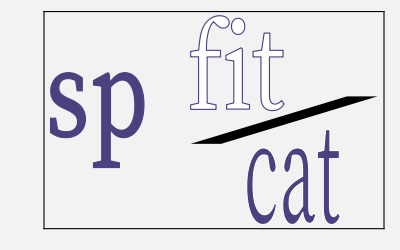
$spIcon=-Graphics-;

Format[SPManager[d_String?DirectoryQ,f_:None]]:=
	RawBoxes@BoxForm`ArrangeSummaryBox[
		"SPManager",
		If[f=!=None,
			SPManager[d,f],
			SPManager@d
			],
		$spIcon,
		{
			Replace[f,None→""]
			},
		{
			BoxForm`MakeSummaryItem[{"Directory: ",
				Button[Hyperlink@FileNameTake@d,
					SystemOpen@d,
					BaseStyle→"Hyperlink",
					Appearance→"Frameless"]
				},StandardForm]
			},
		StandardForm
		];

SPio

$spIOicon=/.GrayLevel[.95]→White;

(*
With[{h=.25,plus=.1,xm=0,xc=.65,aw=.015,xM=1,yc1=.825,yc2=.125,
ims=32,spgraphic=$spIcon},
Graphics[{
EdgeForm@GrayLevel[.8],
FaceForm@GrayLevel[.95],
Polygon@{
{xm,yc1+h/2},{aw+xc,yc1+h/2},{xc,yc1+h/2+plus},
{xM,yc1},
{xc,yc1-h/2-plus},{aw+xc,yc1-h/2},{xm,yc1-h/2},
{xm+plus/2,yc1}
},
Polygon@{
{(xM-xc),yc2-h/2-plus},{(xM-xc)-aw,yc2-h/2},{xM,yc2-h/2},
{xM-plus/2,yc2},
{xM,yc2+h/2},{(xM-xc)-aw,yc2+h/2},{(xM-xc),yc2+h/2+plus},
{xm,yc2}
},
Inset[
Show[spgraphic,ImageSize→.9*{ims,ims}],
{Mean@{xm,xM},Mean@{yc1,yc2}}]
},
PlotRange→{{xm,xM},{yc2-h,yc1+h}},
ImageSize→{ims,ims}
]
];*)

spWriteTemp[a_,parameter_]:=
	Replace[a[parameter],{
		s_String:>
			Button[
				MouseAppearance[
					Mouseover[
						Style[parameter,"Hyperlink"],
						Style[parameter,"HyperlinkActive"]
						],
					"Arrow"
					],
				With[{new=
					ExpandFileName@
					If[StringLength@ToString@a[parameter]>0&&
						(
						FileExistsQ@ToString@a[parameter]||
						(
						FileExistsQ@
							FileNameJoin@{
								Lookup[a,"Directory","-- Failed --"],
								ToString@a[parameter]
								}&&
						!DirectoryQ@
							FileNameJoin@{
								Lookup[a,"Directory","-- Failed --"],
								ToString@a[parameter]
								}
							)
							),
						If[FileExistsQ@a[parameter],
							a[parameter],
							FileNameJoin@{a["Directory"],a[parameter]}
							],
						With[{f=
							OpenWrite@
								FileNameJoin@{
									$TemporaryDirectory,
									Lookup[a,"NAME",parameter]<>"."<>ToLowerCase@parameter
									}
								},
							WriteString[f,s];
							Close@f
							]
						]},
						Switch[$OperatingSystem,
							"MacOSX",
								If[
									RunProcess[{"open","-a","TextWrangler",new}]["ExitCode"]=!=0,
									RunProcess[{"open","-t",new}]
									],
							"Windows",
								If[
									RunProcess[{"pspad",new}]["ExitCode"]=!=0,
									RunProcess[{"Notepad",new}]
									];
								,
							_,
								NotebookOpen@new
							];
						If[
							StringLength@ToString@a[parameter]==0||
							!FileExistsQ@ToString@a[parameter],
							Pause[1];
							DeleteFile@new
							]
					],
				Appearance→"Frameless",
				BaseStyle→"Hyperlink"
				],
		_→None
		}];

dialogTmpOpen[t_,s_]:=
	Button[
		MouseAppearance[
			Mouseover[
				Style[t,"Hyperlink"],
				Style[t,"HyperlinkActive"]
				],
			"Arrow"
			],
		CreateDialog[
			Panel@
				Framed[
					Pane[s,{500,500},Scrollbars→Automatic],
					Background→White,
					FrameStyle→GrayLevel[.8]
					],
			WindowClickSelect→True,
			WindowTitle→t,
			Deployed→False,
			Selectable→True,
			Editable→False
			],
		Appearance→"Frameless",
		BaseStyle→"Hyperlink"
		];

Format[SPio[a_Association]]:=
	RawBoxes@BoxForm`ArrangeSummaryBox[
		"SPio",
		SPio[a],
		$spIOicon,
		{
			Replace[a["NAME"],{
				_Missing:>Nothing,
				e_:>
					BoxForm`MakeSummaryItem[{"Name: ",e},StandardForm]
				}],
			Replace[a["Directory"],{
				_Missing:>Nothing,
				e_:>
					BoxForm`MakeSummaryItem[{"Directory: ",
						Button[Hyperlink@FileNameTake@e,
							SystemOpen@e,
							Appearance→"Frameless",
							BaseStyle→"Hyperlink"]
						},StandardForm]
				}],
			Replace[a["ExitCode"],{
				_Missing:>Nothing,
				e_:>
					BoxForm`MakeSummaryItem[{"Exit code: ",e},StandardForm]
				}],
			If[KeyMemberQ[a,"NAME"|"ExitCode"|"Directory"],
				Nothing,
				"- Input Files -"
				]
			},
		{
			Replace[a["StandardOutput"],{
				_Missing|"":>Nothing,
				e_:>dialogTmpOpen["Output Messages",e]
				}],
			Replace[a["StandardError"],{
				_Missing|"":>Nothing,
				e_:>dialogTmpOpen["Error Messages",e]
				}],
			If[KeyMemberQ[a,"FIT"],
				BoxForm`MakeSummaryItem[{"Fit: ",spWriteTemp[a,"FIT"]},StandardForm],
				Nothing],
			If[KeyMemberQ[a,"VAR"],
				BoxForm`MakeSummaryItem[{"Var: ",spWriteTemp[a,"VAR"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"PAR"],
				BoxForm`MakeSummaryItem[{"Par: ",spWriteTemp[a,"PAR"]},StandardForm],
				Nothing],
			If[KeyMemberQ[a,"LIN"],
				BoxForm`MakeSummaryItem[{"Lin: ",spWriteTemp[a,"LIN"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"INT"],
				BoxForm`MakeSummaryItem[{"Int: ",spWriteTemp[a,"INT"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"CAT"],
				BoxForm`MakeSummaryItem[{"Cat: ",spWriteTemp[a,"CAT"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"EGY"],
				BoxForm`MakeSummaryItem[{"Egy: ",spWriteTemp[a,"EGY"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"STR"],
				BoxForm`MakeSummaryItem[{"Str: ",spWriteTemp[a,"STR"]},StandardForm],
				Nothing
				],
			If[KeyMemberQ[a,"OUT"],
				BoxForm`MakeSummaryItem[{"Out: ",spWriteTemp[a,"OUT"]},StandardForm],
				Nothing
				]
			},
		StandardForm
		];

Imports

LIN

spimportLIN[file:_String?FileExistsQ|_InputStream]:=
	spimportLINTable@Import[file,"Table"];
spimportLINTable[data_]:=
	<|
		"Frequencies"->data[[All,-3]],
		"Errors"->data[[All,-2]],
		"Weights"->data[[All,-1]],
		"Transitions"->data[[All,;;-4]]
		|>;

PAR

spimportPAR[file:_String?FileExistsQ|_InputStream]:=
	With[{f=Replace[file,_String:>OpenRead@file]},
		With[{
			headers=ReadList[f,String,3]},
			With[{data=Import[f,"Table"]},
				Switch[file,_String,Close@f];
				spimportPARTable@
					Join[{
						headers[[1]],
						Flatten@Map[
							ImportString[StringTrim[#,","],"Table"]&,
							StringSplit[headers[[2]],","]
							],
						Flatten@Map[
							ImportString[StringTrim[#,","],"Table"]&,
							StringSplit[headers[[3]],","]
							]
						},
						Rest@data
						]
				]
			]
		];
spimportPARTable[data_]:=
	If[MatchQ[data,{_String,_List,_List,__List}],
		With[{
			line1=data[[1]],
			line2=PadRight[DeleteCases[data[[2]],","],8,None],
			line3=PadRight[DeleteCases[data[[3]],","],12,None],
			parBlock=Cases[data[[4;;]],{_Integer,_Real,__}]
			},
			
			<|
				"Header"→line1,
				
				"ParameterNumber"→line2[[1]],
				"ExtraQuanta"→(line2[[2]]<0),
				"MaxLines"→Abs@line2[[2]],
				"AllowDiagnostics"→(line2[[3]]<0),
				"MaxIterations"→Abs@line2[[3]],
				"ExcludedParameters"→line2[[4]],
				"MarquardtLevenburgThreshold"→line2[[5]],
				"ErrorMax"→line2[[6]],
				"VarianceImportance"→line2[[7]],
				"InfraredScaling"→line2[[8]],
				
				Replace[
					line3[[1]],{
						Except[_String]→Nothing,
						e_:>("WatsonSet"→First@StringCases[e,LetterCharacter])
						}
					],
				Replace[
					line3[[2]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("SymmetricRotor"→(e<0))
						}
					],
				Replace[
					line3[[2]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("SpinDegeneracies"→(Abs@e))
						}
					],
				Replace[
					line3[[3]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("ProlateRotor"→(e≥0))
						}
					],
				Replace[
					line3[[3]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("VibrationalStates"→(Abs@e))
						}
					],
				Replace[
					line3[[4]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("MinKValue"→(e))
						}
					],
				Replace[
					line3[[5]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("MaxKValue"→(e))
						}
					],
				Replace[
					line3[[6]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("IncludedInteractions"→e)
						}
					],
				Replace[
					line3[[7]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("UseInertialBasis"→(e<0))
						}
					],
				Replace[
					line3[[7]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("PrimaryAxis"→(Abs@e))
						}
					],
				Replace[
					line3[[8]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("OddStateWeighting"→(e))
						}
					],
				Replace[
					line3[[9]],{
						Except[_?(NumericQ)]→Nothing,
						e_:>("EvenStateWeighting"→(e))
						}
					],
						
				"ParameterList"→
					Map[<|
						"ID"→Abs@#[[1]],
						"RatioLocked"→#[[1]]<0,
						"Value"→#[[2]],
						"Error"→#[[3]],
						"Label"→If[Length@#>3,StringTrim[#[[4]],StartOfString~~"/"],None]
						|>&,parBlock
						]
					|>
		],
	$Failed
	];

CAT

spimportCAT[f:_String?FileExistsQ|_InputStream]:=
	spimportCAT@Import[f,"Text"];
spimportCAT[string_String]:=
	Merge[
		Replace[
			StringTake[StringSplit[string,"
"],
				{
					{1,13},{14,21},{22,29},
					{30,31},{32,41},{42,44},
					{45,51},{52,55},
					{56,57},{58,59},{60,61},{62,63},{64,65},{66,67},
					{68,69},{70,71},{72,73},{74,75},{76,77},{78,79}
					}
					],
			{
				{frq_,err_,lgnt_,dof_,elo_,gup_,tag_,qft_,
					u1_,u2_,u3_,u4_,u5_,u6_,
					l1_,l2_,l3_,l4_,l5_,l6_}:>
					Replace[{
						Power[s_,t_]:>(Power[s,ToExpression@t]),
						s_String?(StringMatchQ[Whitespace]|""):>Null,
						l_List:>
							Map[Quiet@Check[ToExpression@#,#]&,
								DeleteCases[l,_String?(StringMatchQ[Whitespace|""])]
								],
						e_String:>(Quiet@Check[ToExpression@e,e])
						}]/@<|
						"Frequencies"→frq,"Errors"→err,"Weights"→10.^lgnt,
						"DegreesOfFreedom"→dof,"LowerStateEnergies"→elo,
						"UpperStateDegeneracies"→gup,"Tags"→Abs@ToExpression@tag,
						"ExperimentalLines"→(ToExpression@tag<0),
						"QuantumNumberFormat"→qft,
						"Transitions"→(
								{
									l1,l2,l3,l4,l5,l6,
									u1,u2,u3,u4,u5,u6
									}
								)
						|>
						
				},
			1],
		Join
		];

INT

spimportINT[f:_String?FileExistsQ|_InputStream]:=
	spimportINT@Import[f,"Text"];
spimportINT[string_String]:=
	With[{lines=StringSplit[string,EndOfLine]},
		With[{
			hline=lines[[1]],
			fline=First@ImportString[lines[[2]],"Table"],
			dipoles=
				Replace[StringSplit[Rest@lines[[2;;]],"/"],
					{s_,l___}:>Join[ImportString[s,"Table"],{l}]
					]
			},
			<|
				"Header"→hline,
				
				"Flags"→SPIntParseFlags@fline[[1]],
				"Tag"→fline[[2]],
				"PartitionFunction"→fline[[3]],
				"MinFQuantum"→fline[[4]],
				"MaxFQuantum"→fline[[5]],
				"LogStrengthCutoff1"→fline[[6]],
				"LogStrengthCutoff2"->fline[[7]],
				"FrequencyLimit"→fline[[8]],
				"Temperature"→fline[[9]],
	
				"DipoleMoments"→
					Replace[dipoles,
						{dip_,val_,l_:""}:>
							<|
								"ID"->SPIntParseID@dip,
								"Value"→val
								"Label"→l
								|>
						1]
				|>
			]
		]

EGY

spimportEGY[f:_String?FileExistsQ|_InputStream]:=
	spimportEGY@Import[f,"Text"];
spimportEGY[string_String]:=
	With[{lines=StringSplit[string,"
"]},
		If[StringMatchQ[StringTake[#,{6}],DigitCharacter],
			Replace[
				StringTake[#,{
					{1,6},{7,11},
					{12,29},{30,47},{48,59},
					{60,-1}
					}],
				{iblk_,indx_,egy_,err_,pmix_,q_}:>
					<|
						"BlockNumber"→ToExpression@iblk,
						"BlockIndex"→ToExpression@indx,
						"Energy"→ToExpression@egy,
						"Error"→ToExpression@err,
						"Mixing"→ToExpression@pmix,
						"QuantumNumbers"→First@ImportString[q,"Table"]
						|>
				],
			#
			]&/@lines
		]

Interactive Version

Viewer main

$dinterfSize={500,500};
$dinterfBorder=Gray;
$dinterfBackground=White;
$dinterfRounding=0;
SPViewer[
	spdir:_String?DirectoryQ:$SPDir,
	initialRun_Association?(KeyMemberQ["CAT"])|
		SPio[initialRun_Association?(KeyMemberQ["CAT"])]
	]:=
	DynamicModule[
		{
			src=initialRun,backups={},
			dir=spdir,out="Automatic",
			name,par,var,lin,int,fit,cat,
			stdout=initialRun["StandardOutput"],
			stderr=initialRun["StandardError"],
			tab,simpleTabCMD,
			runTab,parTab,varTab,linTab,fitTab,
			catTab,intTab,
			saveCMD,runCMD,backupCMD,revertCMD,
			backupPos=1
			},
			(*----INITIALIZE----*)
			name=src["NAME"];
			par=src["PAR"];
			var=src["VAR"];
			lin=src["LIN"];
			int=src["INT"];
			fit=src["FIT"];
			cat=src["CAT"];
			(*----BACKUP----*)
			backupCMD[]:=
				AppendTo[backups,
					backupPos=1;
					Now->
						<|
							"NAME"→name,
							"VAR"→var,
							"PAR"→par,
							"LIN"→lin,
							"FIT"→fit,
							"INT"→int,
							"CAT"→cat
							|>];
			(*----REVERT TO PREVIOUS BACKUP----*)
			revertCMD[n_:1,scan:True|False:True]:=
				With[{d=Last@backups[[-Abs@n]]},
					If[
						lin!=d["LIN"]||var!=d["VAR"]||par!=d["PAR"]||
						int≠d["INT"]||fit≠d["FIT"]||cat≠d["CAT"],
						If[
							AllTrue[Last/@backups,
								lin≠#["LIN"]||var≠#["VAR"]||par≠#["PAR"]||
								int≠d["INT"]&
								],
							backupCMD[]
							];
						backupPos=n;
						fit=d["FIT"];
						var=d["VAR"];
						par=d["PAR"];
						lin=d["LIN"];
						cat=d["CAT"];
						int=d["INT"],
						If[scan&&Length@backups<Abs@n,
							revertCMD[n+1]
							];
						]
					];
			(*----SAVE TO DIRECTORY----*)
			saveCMD[]:=
				With[{d=
					If[out==="Automatic"||!DirectoryQ@out,
						SystemDialogInput["Directory"],
						out]},
					If[MatchQ[d,_String?DirectoryQ],
						With[{f=OpenWrite[FileNameJoin@{d,name,".lin"}]},
							WriteString[f,lin];Close@f];
						With[{f=OpenWrite[FileNameJoin@{d,name,".par"}]},
							WriteString[f,par];Close@f];
						With[{f=OpenWrite[FileNameJoin@{d,name,".var"}]},
							WriteString[f,var];Close@f];
						With[{f=OpenWrite[FileNameJoin@{d,name,".fit"}]},
							WriteString[f,fit];Close@f];
						With[{f=OpenWrite[FileNameJoin@{d,name,".cat"}]},
							WriteString[f,cat];Close@f];
						With[{f=OpenWrite[FileNameJoin@{d,name,".int"}]},
							WriteString[f,int];Close@f];
						Export[FileNameJoin@{d,name<>"_backups",".m"},backups];
						]
					];
			(*----RUN CURRENT FILES----*)
			runCMD[]:=(
				backupCMD[];
				stdout=stderr=None;
				With[{a=
					SPManager[dir][
						If[out=="Automatic",Automatic,
							If[Not@DirectoryQ@out,CreateDirectory@out];
							out
							],
							<|
								"NAME"→name,
								"PAR"→par,
								"LIN"→lin,
								"VAR"→var,
								"INT"→int
								|>]},
					tab=1;
					stdout=a["StandardOutput"];
					stderr=a["StandardError"];
					par=a["PAR"];
					var=a["VAR"];
					lin=a["LIN"];
					fit=a["FIT"];
					cat=a["CAT"];
					int=a["INT"];
					]
				);
			(*----RUN TAB----*)
			runTab=
				With[{
					(*----SPCAT/SPFIT DIR INPUT FIELD----*)
					spd=
						Labeled[
							InputField[Dynamic@dir,String],
							"SPCAT/SPFIT Directory",
							{Top,Left}],
					(*----OUTPUT DIR INPUT FIELD----*)
					outd=
						Labeled[
							InputField[Dynamic@out,String],
							"Output Directory",
							{Top,Left}],
					(*----RUN BUTTON----*)
					runb=
						Button["Run",
							runCMD[]
							],
					(*----DISPLAY OUTPUT MESSAGES----*)
					outmb=
						Button["Output Messages",
							If[stdout=!=None,
								CreateDialog[
									Framed[
										Pane[
											Column@stdout,$dinterfSize,
											Scrollbars→Automatic],
										FrameStyle→Gray,
										Background→White],
									WindowTitle→"SP- Output"
									]
								]
							],
					(*----DISPLAY ERROR MESSAGES----*)
					errmb=
						Button["Error Messages",
							If[stderr=!=None,
								CreateDialog[
									Framed[
										Pane[
											Column@stderr,$dinterfSize,
											Scrollbars→Automatic],
										FrameStyle→Gray,
										Background→White],
									WindowTitle→"SP- Errors"
									]
								]
							],
					(*----SAVE----*)
					saveb=
						Button["Save",
							saveCMD[],
							Method→"Queued"
							],
					(*----REVERT TO----*)
					bktob=
						Button["Revert to...",
							If[Length@backups>0,
								With[{j=
									DialogInput[
										Panel@Pane[
											Column@
												Reverse@
													Table[With[{i=i},
														Button[
															backups[[i,1]],
															DialogReturn@(Length@backups-i),
															Appearance→"Palette"]
														],
														{i,Length@backups}
													]
											],
										WindowTitle→"Choose saved state..."
										]},
									If[MatchQ[j,_Integer],revertCMD[j]]
									]
								],
							Method->"Queued"
							],
					(*----REVERT LAST----*)
					bckpb=
						Button["Revert Previous",
							If[Length@backups>0,
								revertCMD[backupPos]
								]
							],
					(*----CAT PLOT----*)
					linplt=
						Dynamic[
							Check[
								EventHandler[
									Tooltip[
									ChemSpectrumPlotDiscrete[
										ChemSpectrumImportString[cat,"CAT"],
										ImageSize→Scaled@1,
										Background→White
										],
									"Double click to pop"
									],
									{
									"MouseClicked":>
										If[CurrentValue@"MouseClickCount"==2,
											CreateDialog@
											ChemSpectrumViewer[
												ChemSpectrumImportString[cat,"CAT"]
												]
											]
										}],
								$Failed
								]
							]
						},
				(*----TAB INTERFACE----*)
				Panel[
					Pane[
						Grid[
							{
								{spd,outd},
								{runb,saveb},
								{bckpb,outmb},
								{bktob,errmb},
								{linplt,SpanFromLeft}
								},
							Dividers→{{},{2->Gray,3→Gray,-2→Gray}}
							],
						$dinterfSize
						]
					]
				];
			(*----TAB MAKE COMMAND----*)
			simpleTabCMD[sym_]:=
				Framed[
					Pane[
						InputField[Dynamic@sym,String,FieldSize→Full,Appearance→"Frameless"],
						$dinterfSize,
						Scrollbars→Automatic,
						BaseStyle→{FontFamily→"Bitstream Vera Sans Mono"}
						],
					Background→$dinterfBackground,
					FrameStyle→$dinterfBorder,
					RoundingRadius→$dinterfRounding
					];
			simpleTabCMD~SetAttributes~HoldFirst;
			(*----PAR TAB----*)
			parTab=simpleTabCMD@par;
			(*----VAR TAB----*)
			varTab=simpleTabCMD@var;
			(*----LIN TAB----*)
			linTab=simpleTabCMD@lin;
			(*----INT TAB----*)
			intTab=simpleTabCMD@int;
			(*----FIT TAB----*)
			fitTab=simpleTabCMD@fit;
			(*----CAT TAB----*)
			catTab=simpleTabCMD@cat;
			(*----DYNAMIC INTERFACE----*)
			tab=1;
			EventHandler[
				TabView[
					{
						"Run"→runTab,
						"PAR"→parTab,
						"VAR"→varTab,
						"LIN"→linTab,
						"INT"→intTab,
						"CAT"→catTab,
						"FIT"→fitTab},
					Dynamic[tab],
					ImageSize→$dinterfSize+{25,25},
					ControlPlacement→{Top,Left}
					],{
				{"MenuCommand","Save"}:>saveCMD[],
				{"MenuCommand","HandleShiftReturn"}:>runCMD[]
				}]
			];

Viewer cmd

SPViewer[
	dir:_String?DirectoryQ:$SPDir,
	a_Association?(Not@*KeyMemberQ["FIT"])]:=
	SPViewer[dir,First@SPManager[dir][a]];

End[];